```mathematica
Pp[x_,0]:=1
Pp[x_,k_]:=Pp[x,k]=Sum[FullSimplify[MangoldtLambda[j]/Log[j]] Pp[x/j,k-1],{j,2,Floor[x]}]
```

```mathematica
Dd[x_, z_] := FullSimplify[Sum[ z^k/k! Pp[x,k],{k,0, Log[2,x]}]]
Cc[x_, z_] := FullSimplify[Sum[ (-1)^k z^(2k)/(2k)! Pp[x,2 k],{k,0, Log[2,x]}]]
Ss[x_, z_] := FullSimplify[Sum[ (-1)^(k-1) z^(2k-1)/(2k-1)! Pp[x,2 k-1],{k,1, Log[2,x]}]]
```

```mathematica
Table[ {Dd[100,n I], Cc[100,n]+ I Ss[100, n]},{n,1,6}]
```

{{-2881/72+(65 ⅈ)/8,-2881/72+(65 ⅈ)/8},{-2029/18-(199 ⅈ)/2,-2029/18-(199 ⅈ)/2},{-557/8-(3241 ⅈ)/8,-557/8-(3241 ⅈ)/8},{2911/9-924 ⅈ,2911/9-924 ⅈ},{98627/72-(12567 ⅈ)/8,98627/72-(12567 ⅈ)/8},{6835/2-(4253 ⅈ)/2,6835/2-(4253 ⅈ)/2}}

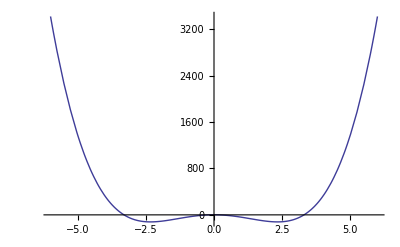

```mathematica
Plot[Cc[100,z ], {z,-6, 6}]
```